```mathematica
a=-1/2;
b=1/2;
l1=1/4;
l2=1/4;
ld=1/2;
L=1;
ke=(G+Gf)/(1000);
kh=(G-Gf)/(1000);
ke1=(G+Gf+Vg)/(1000);
kh1=(G-Gf-Vg)/(1000);
eo1u=1;
ho1d=0;
ei2u=0;
hi2d=0;
γ1=γ2=γ;
ϵ=0.5;
Vg=0;
Z= (GM  - G - I*γ )*(GM+G + I*γ );
x = γ*(G + I*γ )/Z;
x1 = γ*(G + I *γ)/Z;
y = GM*γ/Z;
P=Solve[{eiLu==(1+I x)*eoLu-y*eiRu+I x*hoLd-y*hiRd,
eoRu==y*eoLu+(1+I x1)*eiRu+y*hoLd+I x1*hiRd,
hiLd==I x*eoLu-y*eiRu+(1+I x)*hoLd-y*hiRd,
hoRd==y*eoLu+I x1*eiRu+y*hoLd+(1+I x1)*hiRd,

ei1u==-(a+b)*eo1u+p*eo3u+p*ei5u,
hi1d==-(a+b)ho1d+p*ho3d+p*hi5d,
ei3u==p*eo1u+a*eo3u+b*ei5u,
hi3d==p*ho1d+a*ho3d+b*hi5d,
eo5u==p*eo1u+b*eo3u+a*ei5u,
ho5d==p*ho1d+b*ho3d+a*hi5d,

eo2u==-(a+b)ei2u+p*ei4u+p*eo6u,
ho2d==-(a+b)hi2d+p*hi4d+p*ho6d,
eo4u==p*ei2u+a*ei4u+b*eo6u,
ho4d==p*hi2d+a*hi4d+b*ho6d,
ei6u==p*ei2u+b*ei4u+a*eo6u,
hi6d==p*hi2d+b*hi4d+a*ho6d,

ei5u==Exp[I*ke*l1]*Exp[-I*ϕ*l1]eiLu,
eoLu==Exp[I*ke*l1]*Exp[I*ϕ*l1]eo5u,
hi5d==Exp[I*kh*l1]*Exp[I*ϕ*l1]hiLd,
hoLd==Exp[I*kh*l1]*Exp[-I*ϕ*l1]ho5d,
eo6u==Exp[I*ke*l2]*Exp[I*ϕ*l2]eoRu,
eiRu==Exp[I*ke*l2]*Exp[-I*ϕ*l2]ei6u,
ho6d==Exp[I*kh*l2]*Exp[-I*ϕ*l2]hoRd,
hiRd==Exp[I*kh*l2]*Exp[I*ϕ*l2]hi6d,
eo3u==Exp[I*ke1*ld]*Exp[I*ϕ*ld]eo4u,
ei4u==Exp[I*ke1*ld]*Exp[-I*ϕ*ld]ei3u,
ho3d==Exp[I*kh1*ld]*Exp[-I*ϕ*ld]ho4d,
hi4d==Exp[I*kh1*ld]*Exp[I*ϕ*ld]hi3d}

,{eiLu,eoLu,eiRu,hoLd,hiRd,eoRu,hiLd,hoRd,ei1u,eo3u,ei5u,hi1d,ho3d,hi5d,ei3u,hi3d,eo5u,ho5d,eo2u,ei4u,eo6u,ho2d,hi4d,ho6d,eo4u,ho4d,ei6u,hi6d}];
ei1u=ei1u/.P[[1]];
hi1d=hi1d/.P[[1]];
eo2u=eo2u/.P[[1]]
ho2d=ho2d/.P[[1]]
```

(4 ⅇ^((ⅈ ϕ)/2) (4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+ⅈ ϕ) G^2 p^2+4 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G^2 p^2+8 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G^2 p^2+8 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) G^2 p^2+4 ⅇ^((ⅈ G)/500+(ⅈ Gf)/500+ⅈ ϕ) G^2 p^2+4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/400+ⅈ ϕ) G^2 p^2-4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+ⅈ ϕ) GM^2 p^2-4 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) GM^2 p^2-8 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) GM^2 p^2-8 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) GM^2 p^2-4 ⅇ^((ⅈ G)/500+(ⅈ Gf)/500+ⅈ ϕ) GM^2 p^2-4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/400+ⅈ ϕ) GM^2 p^2-2 ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) G p^2 γ+4 ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+ⅈ ϕ) G p^2 γ-4 ⅈ ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+ⅈ ϕ) G p^2 γ+8 ⅈ ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G p^2 γ-2 ⅈ ⅇ^((ⅈ G)/400+(3 ⅈ Gf)/2000+ⅈ ϕ) G p^2 γ+8 ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) G p^2 γ-4 ⅈ ⅇ^((ⅈ G)/500+(ⅈ Gf)/500+ⅈ ϕ) G p^2 γ+ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000) GM p^2 γ+2 ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000) GM p^2 γ+ⅇ^((ⅈ G)/400+(3 ⅈ Gf)/2000) GM p^2 γ-ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) GM p^2 γ-4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+2 ⅈ ϕ) GM p^2 γ-2 ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+2 ⅈ ϕ) GM p^2 γ-4 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) GM p^2 γ-ⅇ^((ⅈ G)/400+(3 ⅈ Gf)/2000+2 ⅈ ϕ) GM p^2 γ+4 ⅇ^((ⅈ G)/500+(ⅈ Gf)/500+2 ⅈ ϕ) GM p^2 γ+4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/400+2 ⅈ ϕ) GM p^2 γ+ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) p^2 γ^2-4 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) p^2 γ^2+4 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) p^2 γ^2-ⅇ^((ⅈ G)/400+(3 ⅈ Gf)/2000+ⅈ ϕ) p^2 γ^2-ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+3 ⅈ ϕ) p^2 γ^2+ⅇ^((ⅈ G)/400+(3 ⅈ Gf)/2000+3 ⅈ ϕ) p^2 γ^2))/(16 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) G^2+16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) G^2+16 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+2 ⅈ ϕ) G^2+16 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) G^2-16 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) GM^2-16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) GM^2-16 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+2 ⅈ ϕ) GM^2-16 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) GM^2-8 ⅈ ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) G γ+16 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) G γ-8 ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) G γ+32 ⅈ ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) G γ+16 ⅈ ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) G γ-8 ⅈ ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) G γ-8 ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+2 ⅈ ϕ) G γ+4 ⅇ^((ⅈ G)/1000+ⅈ ϕ) GM γ+4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) GM γ-4 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) GM γ-4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) GM γ-4 ⅇ^((ⅈ G)/1000+3 ⅈ ϕ) GM γ-4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+3 ⅈ ϕ) GM γ+4 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+3 ⅈ ϕ) GM γ+4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+3 ⅈ ϕ) GM γ+ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000) γ^2+4 ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) γ^2-16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) γ^2+8 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+2 ⅈ ϕ) γ^2-2 ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+2 ⅈ ϕ) γ^2+4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+2 ⅈ ϕ) γ^2+ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+4 ⅈ ϕ) γ^2)

-((4 ⅇ^((ⅈ G)/2000) γ (-ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) G p^2+ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+ⅈ ϕ) G p^2-ⅈ ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+ⅈ ϕ) G p^2+2 ⅈ ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G p^2+ⅈ ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G p^2+2 ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) G p^2+2 ⅈ ⅇ^((ⅈ G)/1000+3 ⅈ ϕ) G p^2+2 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+3 ⅈ ϕ) G p^2+ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+3 ⅈ ϕ) G p^2+ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+3 ⅈ ϕ) G p^2-ⅈ ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+3 ⅈ ϕ) G p^2-ⅈ ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+3 ⅈ ϕ) G p^2-2 ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) GM p^2+2 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) GM p^2-2 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) GM p^2+4 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) GM p^2+2 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) GM p^2-2 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) GM p^2-2 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+2 ⅈ ϕ) GM p^2+ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) p^2 γ-2 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) p^2 γ+ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) p^2 γ-2 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+3 ⅈ ϕ) p^2 γ+ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+3 ⅈ ϕ) p^2 γ+ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+3 ⅈ ϕ) p^2 γ))/(16 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) G^2+16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) G^2+16 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+2 ⅈ ϕ) G^2+16 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) G^2-16 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) GM^2-16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) GM^2-16 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+2 ⅈ ϕ) GM^2-16 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) GM^2-8 ⅈ ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) G γ+16 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) G γ-8 ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) G γ+32 ⅈ ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) G γ+16 ⅈ ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) G γ-8 ⅈ ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) G γ-8 ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+2 ⅈ ϕ) G γ+4 ⅇ^((ⅈ G)/1000+ⅈ ϕ) GM γ+4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) GM γ-4 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) GM γ-4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) GM γ-4 ⅇ^((ⅈ G)/1000+3 ⅈ ϕ) GM γ-4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+3 ⅈ ϕ) GM γ+4 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+3 ⅈ ϕ) GM γ+4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+3 ⅈ ϕ) GM γ+ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000) γ^2+4 ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) γ^2-16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) γ^2+8 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+2 ⅈ ϕ) γ^2-2 ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+2 ⅈ ϕ) γ^2+4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+2 ⅈ ϕ) γ^2+ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+4 ⅈ ϕ) γ^2))

```mathematica
Te=Refine[eo2u]/.{p->Sqrt[1/2]}//Simplify
```

(2 ⅇ^((ⅈ (G+Gf+1000 ϕ))/2000) (4 ⅇ^((ⅈ (G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2)-4 ⅈ ⅇ^((ⅈ (3 G+Gf+2000 ϕ))/2000) G γ+ⅇ^((ⅈ G)/1000) GM γ+ⅇ^((ⅈ (2 G+Gf))/1000) GM γ+2 ⅇ^((ⅈ (3 G+Gf))/2000) GM γ-ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) GM γ-4 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) GM γ-ⅇ^((ⅈ (2 G+Gf+2000 ϕ))/1000) GM γ+4 ⅇ^((ⅈ (G+2 Gf+2000 ϕ))/1000) GM γ-4 ⅇ^((ⅈ (G+Gf+4000 ϕ))/2000) GM γ-2 ⅇ^((ⅈ (3 G+Gf+4000 ϕ))/2000) GM γ+4 ⅇ^((ⅈ (3 G+3 Gf+4000 ϕ))/2000) GM γ+ⅇ^((ⅈ (2 G+Gf+1000 ϕ))/1000) (-2 ⅈ G-γ) γ-ⅇ^((ⅈ G)/1000+3 ⅈ ϕ) γ^2+ⅇ^((ⅈ (2 G+Gf+3000 ϕ))/1000) γ^2+ⅇ^((ⅈ G)/1000+ⅈ ϕ) γ (-2 ⅈ G+γ)+4 ⅇ^((ⅈ (3 G+3 Gf+2000 ϕ))/2000) (G^2-GM^2-ⅈ G γ)+4 ⅇ^((ⅈ (G+Gf+2000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)+8 ⅇ^((ⅈ (G+3 Gf+2000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)+4 ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) (G^2-GM^2+2 ⅈ G γ-γ^2)+4 ⅇ^((ⅈ (G+Gf+1000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))/(-8 ⅈ ⅇ^((ⅈ (3 G+Gf+4000 ϕ))/2000) G γ-8 ⅈ ⅇ^((ⅈ (3 G+3 Gf+4000 ϕ))/2000) G γ+4 ⅇ^((ⅈ G)/1000+ⅈ ϕ) GM γ-4 ⅇ^((ⅈ G)/1000+3 ⅈ ϕ) GM γ+4 ⅇ^((3 ⅈ (G+Gf+2000 ϕ))/2000) GM γ+4 ⅇ^((ⅈ (3 G+Gf+2000 ϕ))/2000) GM γ-4 ⅇ^((ⅈ (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 ⅇ^((ⅈ (G+2 Gf+3000 ϕ))/1000) GM γ-4 ⅇ^((ⅈ (3 G+Gf+6000 ϕ))/2000) GM γ-4 ⅇ^((ⅈ (G+2 (Gf+500 ϕ)))/1000) GM γ+ⅇ^((ⅈ (2 G+Gf))/1000) γ^2-2 ⅇ^((ⅈ (2 G+Gf+2000 ϕ))/1000) γ^2+ⅇ^((ⅈ (2 G+Gf+4000 ϕ))/1000) γ^2+4 ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) γ (-2 ⅈ G+γ)+4 ⅇ^((ⅈ (G+2 Gf+2000 ϕ))/1000) γ (-2 ⅈ G+γ)+16 ⅇ^((ⅈ (G+Gf+4000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)+16 ⅇ^((ⅈ (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)+16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) (G^2-GM^2+2 ⅈ G γ-γ^2)+8 ⅇ^((ⅈ (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))

```mathematica
Th=Refine[ho2d]/.{p->Sqrt[1/2]}//Simplify
```

(2 ⅇ^((ⅈ G)/2000+ⅈ ϕ) γ (-ⅈ ⅇ^((ⅈ (G+Gf))/1000) G+ⅈ ⅇ^((ⅈ (2 G+Gf))/1000) G-2 ⅈ ⅇ^((ⅈ (G+2 Gf))/1000) G-2 ⅈ ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) G-ⅈ ⅇ^((ⅈ (G+Gf+2000 ϕ))/1000) G+ⅈ ⅇ^((ⅈ (2 G+Gf+2000 ϕ))/1000) G+2 ⅇ^((ⅈ G)/1000+ⅈ ϕ) GM-4 ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) GM-2 ⅇ^((ⅈ (G+Gf+2000 ϕ))/2000) GM+2 ⅇ^((ⅈ (3 G+Gf+2000 ϕ))/2000) GM-2 ⅇ^((ⅈ (G+3 Gf+2000 ϕ))/2000) GM+2 ⅇ^((ⅈ (3 G+3 Gf+2000 ϕ))/2000) GM+2 ⅇ^((ⅈ (G+2 (Gf+500 ϕ)))/1000) GM+ⅇ^((3 ⅈ (G+Gf))/2000) (-ⅈ G-γ)+ⅇ^((ⅈ (3 G+Gf+4000 ϕ))/2000) (-ⅈ G-γ)+ⅈ ⅇ^((ⅈ (3 G+Gf))/2000) (G+ⅈ γ)+ⅈ ⅇ^((ⅈ (3 G+3 Gf+4000 ϕ))/2000) (G+ⅈ γ)+2 ⅇ^((ⅈ (G+3 Gf))/2000) (-ⅈ G+γ)+2 ⅇ^((ⅈ (G+Gf+4000 ϕ))/2000) (-ⅈ G+γ)))/(-8 ⅈ ⅇ^((ⅈ (3 G+Gf+4000 ϕ))/2000) G γ-8 ⅈ ⅇ^((ⅈ (3 G+3 Gf+4000 ϕ))/2000) G γ+4 ⅇ^((ⅈ G)/1000+ⅈ ϕ) GM γ-4 ⅇ^((ⅈ G)/1000+3 ⅈ ϕ) GM γ+4 ⅇ^((3 ⅈ (G+Gf+2000 ϕ))/2000) GM γ+4 ⅇ^((ⅈ (3 G+Gf+2000 ϕ))/2000) GM γ-4 ⅇ^((ⅈ (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 ⅇ^((ⅈ (G+2 Gf+3000 ϕ))/1000) GM γ-4 ⅇ^((ⅈ (3 G+Gf+6000 ϕ))/2000) GM γ-4 ⅇ^((ⅈ (G+2 (Gf+500 ϕ)))/1000) GM γ+ⅇ^((ⅈ (2 G+Gf))/1000) γ^2-2 ⅇ^((ⅈ (2 G+Gf+2000 ϕ))/1000) γ^2+ⅇ^((ⅈ (2 G+Gf+4000 ϕ))/1000) γ^2+4 ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) γ (-2 ⅈ G+γ)+4 ⅇ^((ⅈ (G+2 Gf+2000 ϕ))/1000) γ (-2 ⅈ G+γ)+16 ⅇ^((ⅈ (G+Gf+4000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)+16 ⅇ^((ⅈ (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)+16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) (G^2-GM^2+2 ⅈ G γ-γ^2)+8 ⅇ^((ⅈ (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))

```mathematica
kbT=1;
T1[GM_,γ_,G_,Gf_,ϕ_]:=Abs[(2 E^((I (G+Gf+1000 ϕ))/2000) (4 E^((I (G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2)-4 I E^((I (3 G+Gf+2000 ϕ))/2000) G γ+E^((I G)/1000) GM γ+E^((I (2 G+Gf))/1000) GM γ+2 E^((I (3 G+Gf))/2000) GM γ-E^((I G)/1000+2 I ϕ) GM γ-4 E^((I Gf)/1000+2 I ϕ) GM γ-E^((I (2 G+Gf+2000 ϕ))/1000) GM γ+4 E^((I (G+2 Gf+2000 ϕ))/1000) GM γ-4 E^((I (G+Gf+4000 ϕ))/2000) GM γ-2 E^((I (3 G+Gf+4000 ϕ))/2000) GM γ+4 E^((I (3 G+3 Gf+4000 ϕ))/2000) GM γ+E^((I (2 G+Gf+1000 ϕ))/1000) (-2 I G-γ) γ-E^((I G)/1000+3 I ϕ) γ^2+E^((I (2 G+Gf+3000 ϕ))/1000) γ^2+E^((I G)/1000+I ϕ) γ (-2 I G+γ)+4 E^((I (3 G+3 Gf+2000 ϕ))/2000) (G^2-GM^2-I G γ)+4 E^((I (G+Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+8 E^((I (G+3 Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+4 E^((I Gf)/1000+I ϕ) (G^2-GM^2+2 I G γ-γ^2)+4 E^((I (G+Gf+1000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2+Abs[(2 E^((I G)/2000+I ϕ) γ (-I E^((I (G+Gf))/1000) G+I E^((I (2 G+Gf))/1000) G-2 I E^((I (G+2 Gf))/1000) G-2 I E^((I G)/1000+2 I ϕ) G-I E^((I (G+Gf+2000 ϕ))/1000) G+I E^((I (2 G+Gf+2000 ϕ))/1000) G+2 E^((I G)/1000+I ϕ) GM-4 E^((I Gf)/1000+I ϕ) GM-2 E^((I (G+Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+Gf+2000 ϕ))/2000) GM-2 E^((I (G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (G+2 (Gf+500 ϕ)))/1000) GM+E^((3 I (G+Gf))/2000) (-I G-γ)+E^((I (3 G+Gf+4000 ϕ))/2000) (-I G-γ)+I E^((I (3 G+Gf))/2000) (G+I γ)+I E^((I (3 G+3 Gf+4000 ϕ))/2000) (G+I γ)+2 E^((I (G+3 Gf))/2000) (-I G+γ)+2 E^((I (G+Gf+4000 ϕ))/2000) (-I G+γ)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2;
df[G_]:=(ⅇ^((G-10)/kbT)/((1+ⅇ^((G-10)/kbT))^2 kbT));
LeTt[GM_,γ_,G_,Gf_,ϕ_]:=( ((G - (Gf))/kbT)^(1)) (T1[GM,γ,G,Gf,ϕ])(df[G]);
LeVv[GM_,γ_,G_,Gf_,ϕ_]:=( ((G- (Gf))/kbT)^(0)) (T1[GM,γ,G,Gf,ϕ])(df[G]);
LhVv[GM_,γ_,G_,Gf_,ϕ_]:=( ((G - (Gf))/kbT)^(1)) (T1[GM,γ,G,Gf,ϕ])(df[G]);
LhTt[GM_,γ_,G_,Gf_,ϕ_]:=( ((G - (Gf))/kbT)^(2)) (T1[GM,γ,G,Gf,ϕ])(df[G]);

LeV[GM_?NumericQ,γ_?NumericQ,Gf_?NumericQ,ϕ_?NumericQ]:= NIntegrate[ LeVv[GM,γ,G,Gf,ϕ], {G, -Infinity, Infinity}];

LeT[GM_?NumericQ,γ_?NumericQ,Gf_?NumericQ,ϕ_?NumericQ]:= NIntegrate[LeTt[GM,γ,G,Gf,ϕ], {G, -Infinity, Infinity}];

LhV[GM_?NumericQ,γ_?NumericQ,Gf_?NumericQ,ϕ_?NumericQ]:= NIntegrate[LhVv[GM,γ,G,Gf,ϕ]        , {G, -Infinity, Infinity}];

LhT[GM_?NumericQ,γ_?NumericQ,Gf_?NumericQ,ϕ_?NumericQ]:= NIntegrate[LhTt[GM,γ,G,Gf,ϕ] , {G, -Infinity, Infinity}];
kappa[GM_,γ_,Gf_,ϕ_]:= ((LeV[GM,γ,Gf,ϕ]*LhT[GM,γ,Gf,ϕ] - LhV[GM,γ,Gf,ϕ]*LeT[GM,γ,Gf,ϕ])/ (LeV[GM,γ,Gf,ϕ]))/3.285;
S[GM_,γ_,Gf_,ϕ_]:= -LeT[GM,γ,Gf,ϕ]/LeV[GM,γ,Gf,ϕ];
z0[GM_,γ_,Gf_,ϕ_]:=11.5Re[ (LeV[GM,γ,Gf,ϕ](S[GM,γ,Gf,ϕ])^2/(kappa[GM,γ,Gf,ϕ]))/(1)];
A1[GM_,γ_,Gf_,ϕ_,x_]:= (4x(1-x))/(2(1+2/z0[GM,γ,Gf,ϕ]+√(1-4x(1-x))));
A2[GM_,γ_,Gf_,ϕ_,x_]:= (4x(1-x))/(2(1+2/z0[GM,γ,Gf,ϕ]-√(1-4x(1-x))));
A3[GM_,γ_,Gf_,ϕ_,x_]:= √(1+z0[GM,γ,Gf,ϕ])(x-1);
A4[GM_,γ_,Gf_,ϕ_,x_]:= (1-x)/(x-(1+1/z0[GM,γ,Gf,ϕ])x^2);
```

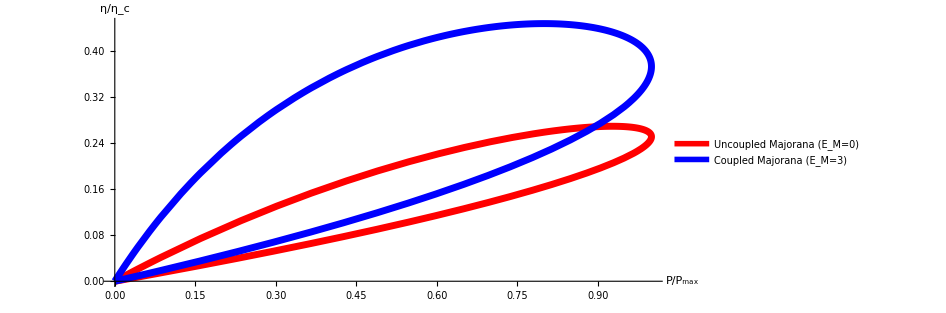
-Graphics-(a)

```mathematica
A5=Labeled[ParametricPlot[{{4x(1-x),Piecewise[{{A1[0,51,10,1.57,x],x<1/2},{A2[0,51,10,1.57,x],x>1/2}}]},{4x(1-x),Piecewise[{{A1[3,51,10,1.57,x],x<1/2},{A2[3,51,10,1.57,x],x>1/2}}]}},{x,0.,1},PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Black]},AxesLabel->{Style["P/P_max",35,Bold,Black],Style["η/η_c",35,Bold,Black]},PlotLegends->Placed[{Style["Uncoupled Majorana (E_M=0)",Bold,25],Style["Coupled Majorana (E_M=3)",Bold,25]},{Center,Center}],AxesStyle->Directive[Black,Bold, 18],ImageSize->700],"(a)",Top,LabelStyle->Directive[Black,Bold,25]]
```

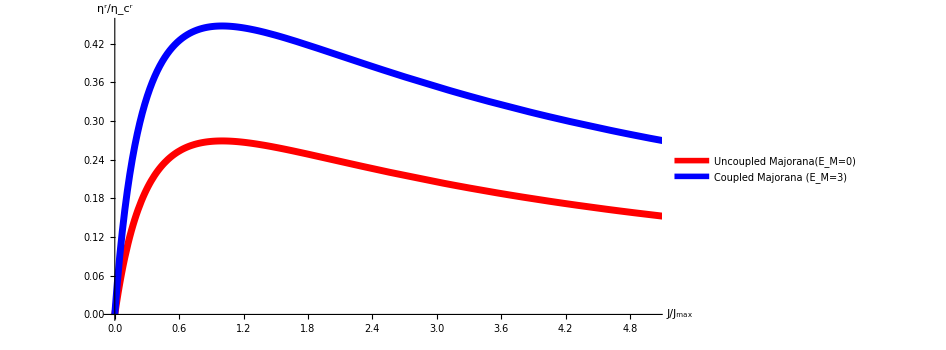
-Graphics-(b)

```mathematica
A6=Labeled[ParametricPlot[{{{A3[0,51,10,1.57,x],A4[0,51,10,1.57,x]}},{{A3[3,51,10,1.57,x],A4[3,51,10,1.57,x]}}},{x,1,30},PlotRange->{{0,5},{0,0.45}},PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Black]},AxesLabel->{Style["J/J_max",35,Bold,Black],Style["η^r/η_c^r",35,Bold,Black]},PlotLegends->Placed[{Style["Uncoupled Majorana(E_M=0)",Bold,25],Style["Coupled Majorana (E_M=3)",Bold,25]},{Center,Center}],AxesStyle->Directive[Black,Bold, 18],ImageSize->700,AspectRatio->1/2],"(b)",Top,LabelStyle->Directive[Black,Bold,25]]
```

```mathematica
kbT=1;
T1=Abs[(2 E^((I (G+Gf+1000 ϕ))/2000) (4 E^((I (G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2)-4 I E^((I (3 G+Gf+2000 ϕ))/2000) G γ+E^((I G)/1000) GM γ+E^((I (2 G+Gf))/1000) GM γ+2 E^((I (3 G+Gf))/2000) GM γ-E^((I G)/1000+2 I ϕ) GM γ-4 E^((I Gf)/1000+2 I ϕ) GM γ-E^((I (2 G+Gf+2000 ϕ))/1000) GM γ+4 E^((I (G+2 Gf+2000 ϕ))/1000) GM γ-4 E^((I (G+Gf+4000 ϕ))/2000) GM γ-2 E^((I (3 G+Gf+4000 ϕ))/2000) GM γ+4 E^((I (3 G+3 Gf+4000 ϕ))/2000) GM γ+E^((I (2 G+Gf+1000 ϕ))/1000) (-2 I G-γ) γ-E^((I G)/1000+3 I ϕ) γ^2+E^((I (2 G+Gf+3000 ϕ))/1000) γ^2+E^((I G)/1000+I ϕ) γ (-2 I G+γ)+4 E^((I (3 G+3 Gf+2000 ϕ))/2000) (G^2-GM^2-I G γ)+4 E^((I (G+Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+8 E^((I (G+3 Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+4 E^((I Gf)/1000+I ϕ) (G^2-GM^2+2 I G γ-γ^2)+4 E^((I (G+Gf+1000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2+Abs[(2 E^((I G)/2000+I ϕ) γ (-I E^((I (G+Gf))/1000) G+I E^((I (2 G+Gf))/1000) G-2 I E^((I (G+2 Gf))/1000) G-2 I E^((I G)/1000+2 I ϕ) G-I E^((I (G+Gf+2000 ϕ))/1000) G+I E^((I (2 G+Gf+2000 ϕ))/1000) G+2 E^((I G)/1000+I ϕ) GM-4 E^((I Gf)/1000+I ϕ) GM-2 E^((I (G+Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+Gf+2000 ϕ))/2000) GM-2 E^((I (G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (G+2 (Gf+500 ϕ)))/1000) GM+E^((3 I (G+Gf))/2000) (-I G-γ)+E^((I (3 G+Gf+4000 ϕ))/2000) (-I G-γ)+I E^((I (3 G+Gf))/2000) (G+I γ)+I E^((I (3 G+3 Gf+4000 ϕ))/2000) (G+I γ)+2 E^((I (G+3 Gf))/2000) (-I G+γ)+2 E^((I (G+Gf+4000 ϕ))/2000) (-I G+γ)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2;
df=(ⅇ^((G-10)/kbT)/((1+ⅇ^((G-10)/kbT))^2 kbT));
γ=51;
GM=0;
ϕ=1;
Gf=10;
SetSharedVariable[list1]
list1={};
ParallelDo[{
LeTt=( ((G - (Gf))/kbT)^(1)) (T1)(df);
LeVv=( ((G- (Gf))/kbT)^(0)) (T1)(df);
LhVv=( ((G - (Gf))/kbT)^(1)) (T1)(df);
LhTt=( ((G - (Gf))/kbT)^(2)) (T1)(df);

LeV= NIntegrate[ LeVv, {G, -Infinity, Infinity}];

LeT= NIntegrate[LeTt, {G, -Infinity, Infinity}];

LhV= NIntegrate[LhVv, {G, -Infinity, Infinity}];

LhT= NIntegrate[LhTt,{G, -Infinity, Infinity}];
kappa= ((LeV*LhT - LhV*LeT)/ (LeV))/3.285;
S= -LeT/LeV;
z0=11.5Re[ (LeV(S)^2/(kappa))/(1)];
A1= Piecewise[{{(4x(1-x))/(2(1+2/z0+√(1-4x(1-x)))),x<=1/2},{(4x(1-x))/(2(1+2/z0-√(1-4x(1-x)))),x>1/2}}];
A2=4x(1-x);
A3= √(1+z0)(x-1);
A4= (1-x)/(x-(1+1/z0)x^2);
list=AppendTo[list1,{x,A2,A1,A3,A4}];
},{x,0,5,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check420.dat",list]
```

Power::infy: Infinite expression 1/0. encountered.

{26.9648,Null}

check420.dat

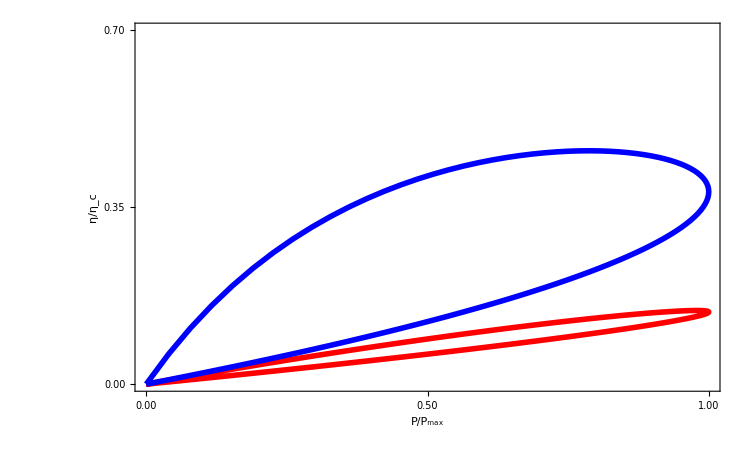

```mathematica
data1=Import["check420.dat"][[All,{2,3}]];
data2=Import["check421.dat"][[All,{2,3}]];
Needs["PlotLegends`"]
A8=ListLinePlot[{data1,data2},Frame->True,PlotRange->{{0,1},{0,0.7}},Frame->{{True,True},{True,True}},
FrameTicks->{{{{0,"0.00"},{0.35,"0.35"},{0.7,"0.70"}},None},{{{0.,"0.00"},{0.5,"0.50"},{1,"1.00"}},None}},
FrameLabel->{{Rotate[Style["η/η_c",50,Bold,Black],-90 Degree],None},{Style["P/P_max",70,Bold,Black],None}},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[4],Opacity[1],Red],Directive[AbsoluteThickness[4],Opacity[1],Blue]},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
A5=Legended[GraphicsGrid[{{A8}},ImageSize->1000],Placed[LineLegend[{Directive[Red,AbsoluteThickness[5]],Directive[Blue,AbsoluteThickness[5]]},{Style["Uncoupled Majorana (E^M=0)",Bold,Black,35],Style["Coupled Majorana (E^M=7μeV)",Bold,Black,35]},LegendFunction->Frame,LegendLayout->"Row",LegendMarkerSize->{70,25}],{0.7,0.9}]]
```

-Graphics-

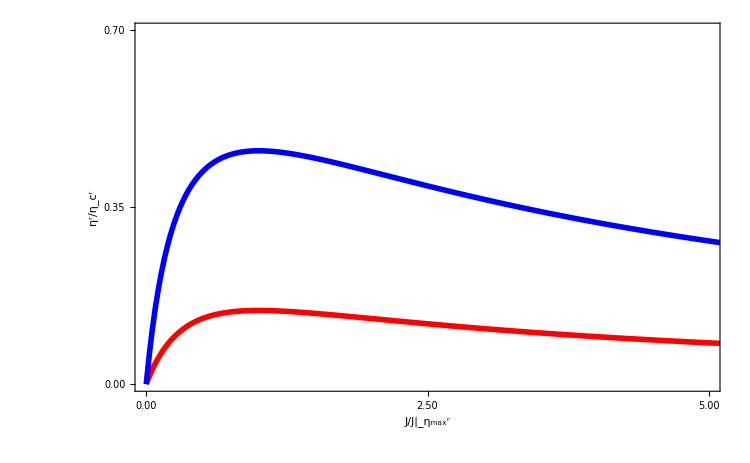

```mathematica
data1=Import["check420.dat"][[All,{4,5}]];
data2=Import["check421.dat"][[All,{4,5}]];
Needs["PlotLegends`"]
A8=ListLinePlot[{data1,data2},Frame->True,PlotRange->{{0,5},{0,0.7}},Frame->{{True,True},{True,True}},
FrameTicks->{{{{0,"0.00"},{0.35,"0.35"},{0.7,"0.70"}},None},{{{0.,"0.00"},{2.5,"2.50"},{5,"5.00"}},None}},
FrameLabel->{{Rotate[Style["η^r/η_c^r",50,Bold,Black],-90 Degree],None},{Style["J/J|_(η_max^r)",70,Bold,Black],None}},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[4],Opacity[1],Red],Directive[AbsoluteThickness[4],Opacity[1],Blue]},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
A5=Legended[GraphicsGrid[{{A8}},ImageSize->1000],Placed[LineLegend[{Directive[Red,AbsoluteThickness[5]],Directive[Blue,AbsoluteThickness[5]]},{Style["Uncoupled Majorana (E^M=0)",Bold,Black,35],Style["Coupled Majorana (E^M=7μeV)",Bold,Black,35]},LegendFunction->Frame,LegendLayout->"Row",LegendMarkerSize->{70,25}],{0.7,0.9}]]
```

-Graphics-

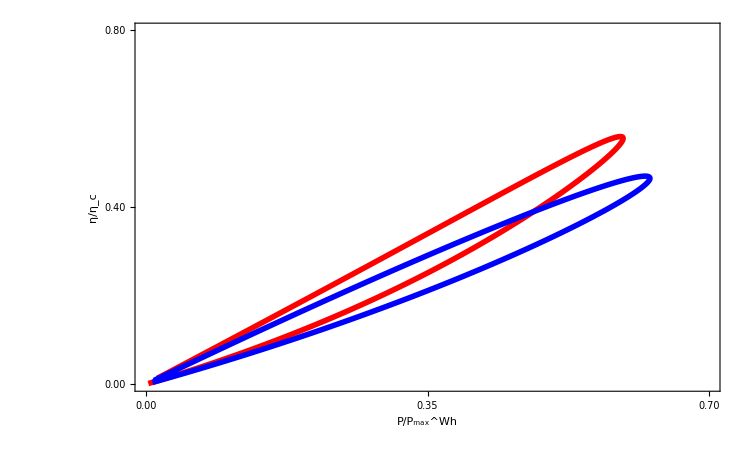

```mathematica
data1=Import["check520.dat"][[All,{3,4}]];
data2=Import["check521.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A8=ListLinePlot[{data1,data2},Frame->True,PlotRange->{{0,0.7},{0,0.8}},Frame->{{True,True},{True,True}},
FrameTicks->{{{{0,"0.00"},{0.40,"0.40"},{0.8,"0.80"}},None},{{{0.,"0.00"},{0.35,"0.35"},{0.7,"0.70"}},None}},
FrameLabel->{{Rotate[Style["η/η_c",50,Bold,Black],-90 Degree],None},{Style["P/P_max^Wh",70,Bold,Black],None}},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[4],Opacity[1],Red],Directive[AbsoluteThickness[4],Opacity[1],Blue]},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
A5=Legended[GraphicsGrid[{{A8}},ImageSize->1000],Placed[LineLegend[{Directive[Red,AbsoluteThickness[5]],Directive[Blue,AbsoluteThickness[5]]},{Style["Uncoupled Majorana (E^M=0)",Bold,Black,35],Style["Coupled Majorana (E^M=7μeV)",Bold,Black,35]},LegendFunction->Frame,LegendLayout->"Row",LegendMarkerSize->{70,25}],{0.7,0.9}]]
```

-Graphics-

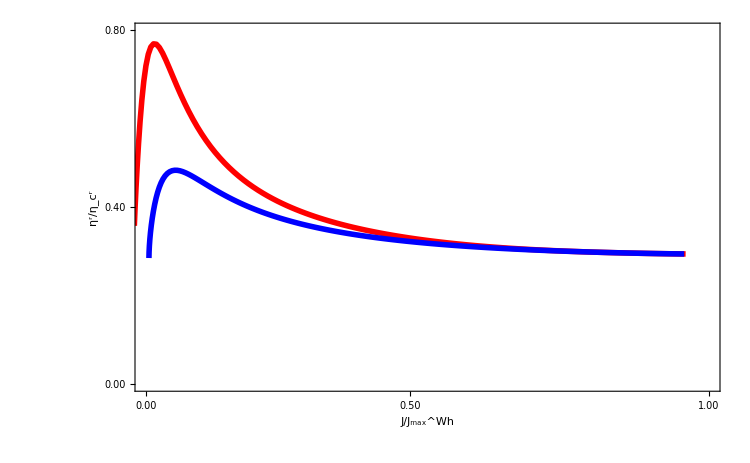

```mathematica
data1=Import["check621.dat"][[All,{3,4}]];
data2=Import["check622.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A8=ListLinePlot[{data1,data2},Frame->True,PlotRange->{{0.059,1},{0,0.8}},Frame->{{True,True},{True,True}},
FrameTicks->{{{{0,"0.00"},{0.40,"0.40"},{0.8,"0.80"}},None},{{{0.059,"0.00"},{0.5,"0.50"},{1,"1.00"}},None}},
FrameLabel->{{Rotate[Style["η^r/η_c^r",50,Bold,Black],-90 Degree],None},{Style["J/J_max^Wh",70,Bold,Black],None}},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[4],Opacity[1],Red],Directive[AbsoluteThickness[4],Opacity[1],Blue]},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
A5=Legended[GraphicsGrid[{{A8}},ImageSize->1000],Placed[LineLegend[{Directive[Red,AbsoluteThickness[5]],Directive[Blue,AbsoluteThickness[5]]},{Style["Uncoupled Majorana (E^M=0)",Bold,Black,35],Style["Coupled Majorana (E^M=7μeV)",Bold,Black,35]},LegendFunction->Frame,LegendLayout->"Row",LegendMarkerSize->{70,25}],{0.7,0.9}]]
```

-Graphics-

```mathematica
a=-1/2;
b=1/2;
l1=1/4;
l2=1/4;
ld=1/2;
L=1;
ke=(G+Gf+Vg)*1000;
kh=(-G-Gf-Vg)*1000;
ke1=(G+Gf+Vg)*1000;
kh1=(-G-Gf-Vg)*1000;
eo1u=1;
ho1d=0;
ei2u=0;
hi2d=0;
γ1=γ2=γ;
ϵ=0.5;
(*Z= (GM  - G-Vg - I*γ )*(GM+G+Vg + I*γ );
x = γ*(G +Vg+I*γ )/Z;
x1 = γ*(G +Vg+ I *γ)/Z;
y = GM*γ/Z;*)
P=Solve[{eiLu==(1+I x)*eoLu-y*eiRu+I x*hoLd-y*hiRd,
eoRu==y*eoLu+(1+I x1)*eiRu+y*hoLd+I x1*hiRd,
hiLd==I x*eoLu-y*eiRu+(1+I x)*hoLd-y*hiRd,
hoRd==y*eoLu+I x1*eiRu+y*hoLd+(1+I x1)*hiRd,

ei1u==-(a+b)*eo1u+p*eo3u+p*ei5u,
hi1d==-(a+b)ho1d+p*ho3d+p*hi5d,
ei3u==p*eo1u+a*eo3u+b*ei5u,
hi3d==p*ho1d+a*ho3d+b*hi5d,
eo5u==p*eo1u+b*eo3u+a*ei5u,
ho5d==p*ho1d+b*ho3d+a*hi5d,

eo2u==-(a+b)ei2u+p*ei4u+p*eo6u,
ho2d==-(a+b)hi2d+p*hi4d+p*ho6d,
eo4u==p*ei2u+a*ei4u+b*eo6u,
ho4d==p*hi2d+a*hi4d+b*ho6d,
ei6u==p*ei2u+b*ei4u+a*eo6u,
hi6d==p*hi2d+b*hi4d+a*ho6d,

ei5u==Exp[I*ke*l1]*Exp[-I*ϕ*l1]eiLu,
eoLu==Exp[I*ke*l1]*Exp[I*ϕ*l1]eo5u,
hi5d==Exp[I*kh*l1]*Exp[I*ϕ*l1]hiLd,
hoLd==Exp[I*kh*l1]*Exp[-I*ϕ*l1]ho5d,
eo6u==Exp[I*ke*l2]*Exp[I*ϕ*l2]eoRu,
eiRu==Exp[I*ke*l2]*Exp[-I*ϕ*l2]ei6u,
ho6d==Exp[I*kh*l2]*Exp[-I*ϕ*l2]hoRd,
hiRd==Exp[I*kh*l2]*Exp[I*ϕ*l2]hi6d,
eo3u==Exp[I*ke1*ld]*Exp[I*ϕ*ld]eo4u,
ei4u==Exp[I*ke1*ld]*Exp[-I*ϕ*ld]ei3u,
ho3d==Exp[I*kh1*ld]*Exp[-I*ϕ*ld]ho4d,
hi4d==Exp[I*kh1*ld]*Exp[I*ϕ*ld]hi3d}

,{eiLu,eoLu,eiRu,hoLd,hiRd,eoRu,hiLd,hoRd,ei1u,eo3u,ei5u,hi1d,ho3d,hi5d,ei3u,hi3d,eo5u,ho5d,eo2u,ei4u,eo6u,ho2d,hi4d,ho6d,eo4u,ho4d,ei6u,hi6d}];
ei1u=ei1u/.P[[1]]//Simplify
hi1d=hi1d/.P[[1]]//Simplify
eo2u=eo2u/.P[[1]]//Simplify
ho2d=ho2d/.P[[1]]//Simplify
```

-((2 ⅇ^(500 ⅈ (G+Gf+Vg)) p^2 (ⅇ^(2 ⅈ (750 G+750 Gf+750 Vg+ϕ)) (8+8 ⅈ x)+ⅇ^(2 ⅈ (1000 G+1000 Gf+1000 Vg+ϕ)) (8+8 ⅈ x)+2 ⅇ^(ⅈ ϕ) y-2 ⅇ^(3 ⅈ ϕ) y-4 ⅇ^(3 ⅈ (500 G+500 Gf+500 Vg+ϕ)) y+2 ⅇ^(ⅈ (1000 G+1000 Gf+1000 Vg+ϕ)) y+4 ⅇ^(ⅈ (1500 G+1500 Gf+1500 Vg+ϕ)) y-2 ⅇ^(ⅈ (1000 G+1000 Gf+1000 Vg+3 ϕ)) y+ⅇ^(2 ⅈ ϕ) (-2 ⅈ x1+x (-2 ⅈ+4 x1)-4 y^2)+2 ⅇ^(2 ⅈ (250 G+250 Gf+250 Vg+ϕ)) (-4-2 ⅈ x1+3 x (-2 ⅈ+x1)-3 y^2)+ⅇ^(500 ⅈ (G+Gf+Vg)) (x x1-y^2)+ⅇ^(4 ⅈ (125 G+125 Gf+125 Vg+ϕ)) (x x1-y^2)+2 ⅇ^(2 ⅈ (500 G+500 Gf+500 Vg+ϕ)) (-ⅈ x1+x (-5 ⅈ+2 x1)-2 (2+y^2))))/(-4 ⅇ^(ⅈ ϕ) y+4 ⅇ^(3 ⅈ ϕ) y-4 ⅇ^(ⅈ (500 G+500 Gf+500 Vg+ϕ)) y-4 ⅇ^(3 ⅈ (500 G+500 Gf+500 Vg+ϕ)) y+4 ⅇ^(ⅈ (1500 G+1500 Gf+1500 Vg+ϕ)) y+4 ⅇ^(ⅈ (2000 G+2000 Gf+2000 Vg+ϕ)) y+4 ⅇ^(ⅈ (500 G+500 Gf+500 Vg+3 ϕ)) y-4 ⅇ^(ⅈ (2000 G+2000 Gf+2000 Vg+3 ϕ)) y+ⅇ^(1000 ⅈ (G+Gf+Vg)) (x x1-y^2)+ⅇ^(4 ⅈ (250 G+250 Gf+250 Vg+ϕ)) (x x1-y^2)+4 ⅇ^(2 ⅈ (250 G+250 Gf+250 Vg+ϕ)) (4+x (3 ⅈ-2 x1)+3 ⅈ x1+2 y^2)+4 ⅇ^(2 ⅈ (750 G+750 Gf+750 Vg+ϕ)) (4+x (3 ⅈ-2 x1)+3 ⅈ x1+2 y^2)+ⅇ^(2 ⅈ ϕ) (4 ⅈ x+4 ⅈ x1-4 x x1+4 y^2)+ⅇ^(2 ⅈ (1000 G+1000 Gf+1000 Vg+ϕ)) (4 ⅈ x+4 ⅈ x1-4 x x1+4 y^2)+2 ⅇ^(2 ⅈ (500 G+500 Gf+500 Vg+ϕ)) (16+x (8 ⅈ-5 x1)+8 ⅈ x1+5 y^2)))

(4 ⅇ^((ⅈ ϕ)/2) (1+ⅇ^(500 ⅈ (G+Gf+Vg)))^2 p^2 (-2 ⅈ ⅇ^(2 ⅈ ϕ) x-2 ⅈ ⅇ^(2 ⅈ (500 G+500 Gf+500 Vg+ϕ)) x+2 ⅇ^(ⅈ ϕ) y-2 ⅇ^(ⅈ (1000 G+1000 Gf+1000 Vg+ϕ)) y+ⅇ^(500 ⅈ (G+Gf+Vg)) (-((-ⅈ+x) x1)+y^2)+ⅇ^(2 ⅈ (250 G+250 Gf+250 Vg+ϕ)) (-x (-5 ⅈ+x1)+y^2)))/(-4 ⅇ^(ⅈ ϕ) y+4 ⅇ^(3 ⅈ ϕ) y-4 ⅇ^(ⅈ (500 G+500 Gf+500 Vg+ϕ)) y-4 ⅇ^(3 ⅈ (500 G+500 Gf+500 Vg+ϕ)) y+4 ⅇ^(ⅈ (1500 G+1500 Gf+1500 Vg+ϕ)) y+4 ⅇ^(ⅈ (2000 G+2000 Gf+2000 Vg+ϕ)) y+4 ⅇ^(ⅈ (500 G+500 Gf+500 Vg+3 ϕ)) y-4 ⅇ^(ⅈ (2000 G+2000 Gf+2000 Vg+3 ϕ)) y+ⅇ^(1000 ⅈ (G+Gf+Vg)) (x x1-y^2)+ⅇ^(4 ⅈ (250 G+250 Gf+250 Vg+ϕ)) (x x1-y^2)+4 ⅇ^(2 ⅈ (250 G+250 Gf+250 Vg+ϕ)) (4+x (3 ⅈ-2 x1)+3 ⅈ x1+2 y^2)+4 ⅇ^(2 ⅈ (750 G+750 Gf+750 Vg+ϕ)) (4+x (3 ⅈ-2 x1)+3 ⅈ x1+2 y^2)+ⅇ^(2 ⅈ ϕ) (4 ⅈ x+4 ⅈ x1-4 x x1+4 y^2)+ⅇ^(2 ⅈ (1000 G+1000 Gf+1000 Vg+ϕ)) (4 ⅈ x+4 ⅈ x1-4 x x1+4 y^2)+2 ⅇ^(2 ⅈ (500 G+500 Gf+500 Vg+ϕ)) (16+x (8 ⅈ-5 x1)+8 ⅈ x1+5 y^2))

(4 ⅇ^(1/2 ⅈ (1000 (G+Gf+Vg)+ϕ)) (1+ⅇ^(500 ⅈ (G+Gf+Vg))) p^2 (-y-ⅇ^(500 ⅈ (G+Gf+Vg)) y+ⅇ^(2 ⅈ ϕ) y+5 ⅇ^(2 ⅈ (250 G+250 Gf+250 Vg+ϕ)) y-4 ⅇ^(2 ⅈ (750 G+750 Gf+750 Vg+ϕ)) y+ⅇ^(ⅈ (500 G+500 Gf+500 Vg+3 ϕ)) (x x1-y^2)+ⅇ^(3 ⅈ ϕ) (-x x1+y^2)+ⅇ^(ⅈ ϕ) (ⅈ x1-x (-ⅈ+x1)+y^2)+ⅇ^(ⅈ (500 G+500 Gf+500 Vg+ϕ)) (4+3 ⅈ x1-3 x (-ⅈ+x1)+3 y^2)+ⅇ^(ⅈ (1000 G+1000 Gf+1000 Vg+ϕ)) (8+x (6 ⅈ-4 x1)+6 ⅈ x1+4 y^2)+ⅇ^(ⅈ (1500 G+1500 Gf+1500 Vg+ϕ)) (4+4 ⅈ x+4 ⅈ x1-4 x x1+4 y^2)))/(-4 ⅇ^(ⅈ ϕ) y+4 ⅇ^(3 ⅈ ϕ) y-4 ⅇ^(ⅈ (500 G+500 Gf+500 Vg+ϕ)) y-4 ⅇ^(3 ⅈ (500 G+500 Gf+500 Vg+ϕ)) y+4 ⅇ^(ⅈ (1500 G+1500 Gf+1500 Vg+ϕ)) y+4 ⅇ^(ⅈ (2000 G+2000 Gf+2000 Vg+ϕ)) y+4 ⅇ^(ⅈ (500 G+500 Gf+500 Vg+3 ϕ)) y-4 ⅇ^(ⅈ (2000 G+2000 Gf+2000 Vg+3 ϕ)) y+ⅇ^(1000 ⅈ (G+Gf+Vg)) (x x1-y^2)+ⅇ^(4 ⅈ (250 G+250 Gf+250 Vg+ϕ)) (x x1-y^2)+4 ⅇ^(2 ⅈ (250 G+250 Gf+250 Vg+ϕ)) (4+x (3 ⅈ-2 x1)+3 ⅈ x1+2 y^2)+4 ⅇ^(2 ⅈ (750 G+750 Gf+750 Vg+ϕ)) (4+x (3 ⅈ-2 x1)+3 ⅈ x1+2 y^2)+ⅇ^(2 ⅈ ϕ) (4 ⅈ x+4 ⅈ x1-4 x x1+4 y^2)+ⅇ^(2 ⅈ (1000 G+1000 Gf+1000 Vg+ϕ)) (4 ⅈ x+4 ⅈ x1-4 x x1+4 y^2)+2 ⅇ^(2 ⅈ (500 G+500 Gf+500 Vg+ϕ)) (16+x (8 ⅈ-5 x1)+8 ⅈ x1+5 y^2))

(4 ⅇ^(ⅈ ϕ) (1+ⅇ^(500 ⅈ (G+Gf+Vg))) p^2 (ⅈ ⅇ^(2 ⅈ (250 G+250 Gf+250 Vg+ϕ)) x-ⅈ ⅇ^(2 ⅈ (500 G+500 Gf+500 Vg+ϕ)) x-ⅈ ⅇ^(500 ⅈ (G+Gf+Vg)) x1+ⅈ ⅇ^(1000 ⅈ (G+Gf+Vg)) x1-2 ⅇ^(ⅈ ϕ) y+2 ⅇ^(ⅈ (500 G+500 Gf+500 Vg+ϕ)) y+2 ⅇ^(ⅈ (1000 G+1000 Gf+1000 Vg+ϕ)) y-2 ⅇ^(ⅈ (1500 G+1500 Gf+1500 Vg+ϕ)) y+ⅇ^(1500 ⅈ (G+Gf+Vg)) (-2 (-ⅈ+x) x1+2 y^2)+ⅇ^(2 ⅈ ϕ) (-2 x (-ⅈ+x1)+2 y^2)))/(-4 ⅇ^(ⅈ ϕ) y+4 ⅇ^(3 ⅈ ϕ) y-4 ⅇ^(ⅈ (500 G+500 Gf+500 Vg+ϕ)) y-4 ⅇ^(3 ⅈ (500 G+500 Gf+500 Vg+ϕ)) y+4 ⅇ^(ⅈ (1500 G+1500 Gf+1500 Vg+ϕ)) y+4 ⅇ^(ⅈ (2000 G+2000 Gf+2000 Vg+ϕ)) y+4 ⅇ^(ⅈ (500 G+500 Gf+500 Vg+3 ϕ)) y-4 ⅇ^(ⅈ (2000 G+2000 Gf+2000 Vg+3 ϕ)) y+ⅇ^(1000 ⅈ (G+Gf+Vg)) (x x1-y^2)+ⅇ^(4 ⅈ (250 G+250 Gf+250 Vg+ϕ)) (x x1-y^2)+4 ⅇ^(2 ⅈ (250 G+250 Gf+250 Vg+ϕ)) (4+x (3 ⅈ-2 x1)+3 ⅈ x1+2 y^2)+4 ⅇ^(2 ⅈ (750 G+750 Gf+750 Vg+ϕ)) (4+x (3 ⅈ-2 x1)+3 ⅈ x1+2 y^2)+ⅇ^(2 ⅈ ϕ) (4 ⅈ x+4 ⅈ x1-4 x x1+4 y^2)+ⅇ^(2 ⅈ (1000 G+1000 Gf+1000 Vg+ϕ)) (4 ⅈ x+4 ⅈ x1-4 x x1+4 y^2)+2 ⅇ^(2 ⅈ (500 G+500 Gf+500 Vg+ϕ)) (16+x (8 ⅈ-5 x1)+8 ⅈ x1+5 y^2))

```mathematica
Te=Refine[eo2u]/.{p->Sqrt[1/2]}//Simplify
```

(2 ⅇ^((ⅈ (G+Gf+Vg+1000 ϕ))/2000) (4 ⅇ^((ⅈ (Gf+Vg+1000 ϕ))/1000)+2 ⅈ ⅇ^((ⅈ (G+Gf+Vg+2000 ϕ))/2000) (-2 ⅈ+x+x1)+4 ⅈ ⅇ^((ⅈ (G+3 Gf+3 Vg+2000 ϕ))/2000) (-2 ⅈ+x+x1)-ⅇ^((ⅈ G)/1000) y-ⅇ^((ⅈ (2 G+Gf+Vg))/1000) y-2 ⅇ^((ⅈ (3 G+Gf+Vg))/2000) y+ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) y+4 ⅇ^((ⅈ (Gf+Vg+2000 ϕ))/1000) y+ⅇ^((ⅈ (2 G+Gf+Vg+2000 ϕ))/1000) y+4 ⅇ^((ⅈ (G+Gf+Vg+4000 ϕ))/2000) y+2 ⅇ^((ⅈ (3 G+Gf+Vg+4000 ϕ))/2000) y-4 ⅇ^((ⅈ (3 G+3 Gf+3 Vg+4000 ϕ))/2000) y-4 ⅇ^((ⅈ (G+2 (Gf+Vg+1000 ϕ)))/1000) y+ⅇ^((ⅈ (2 G+Gf+Vg+3000 ϕ))/1000) (x x1-y^2)+ⅇ^((ⅈ G)/1000+3 ⅈ ϕ) (-x x1+y^2)+ⅇ^((ⅈ G)/1000+ⅈ ϕ) (ⅈ x1-x (-ⅈ+x1)+y^2)+ⅇ^((ⅈ (2 G+Gf+Vg+1000 ϕ))/1000) (x (ⅈ-3 x1)+ⅈ x1+3 y^2)+ⅇ^((ⅈ (3 G+Gf+Vg+2000 ϕ))/2000) (x (2 ⅈ-4 x1)+2 ⅈ x1+4 y^2)+ⅇ^((ⅈ (G+2 (Gf+Vg+500 ϕ)))/1000) (4+4 ⅈ x+4 ⅈ x1-4 x x1+4 y^2)+ⅇ^((ⅈ (G+Gf+Vg+1000 ϕ))/1000) (8+8 ⅈ x+8 ⅈ x1-4 x x1+4 y^2)+ⅇ^((ⅈ (3 G+3 Gf+3 Vg+2000 ϕ))/2000) (4+x (6 ⅈ-8 x1)+6 ⅈ x1+8 y^2)))/(16 ⅇ^((ⅈ (Gf+Vg+2000 ϕ))/1000)+8 ⅈ ⅇ^((ⅈ (G+Gf+Vg+4000 ϕ))/2000) (-2 ⅈ+x+x1)+8 ⅈ ⅇ^((ⅈ (G+3 Gf+3 Vg+4000 ϕ))/2000) (-2 ⅈ+x+x1)-4 ⅇ^((ⅈ G)/1000+ⅈ ϕ) y+4 ⅇ^((ⅈ G)/1000+3 ⅈ ϕ) y-4 ⅇ^((3 ⅈ (G+Gf+Vg+2000 ϕ))/2000) y-4 ⅇ^((ⅈ (3 G+Gf+Vg+2000 ϕ))/2000) y+4 ⅇ^((ⅈ (3 G+3 Gf+3 Vg+2000 ϕ))/2000) y+4 ⅇ^((ⅈ (3 G+Gf+Vg+6000 ϕ))/2000) y+4 ⅇ^((ⅈ (G+2 (Gf+Vg+500 ϕ)))/1000) y-4 ⅇ^((ⅈ (G+2 (Gf+Vg+1500 ϕ)))/1000) y+ⅇ^((ⅈ (2 G+Gf+Vg))/1000) (x x1-y^2)+ⅇ^((ⅈ (2 G+Gf+Vg+4000 ϕ))/1000) (x x1-y^2)+8 ⅇ^((ⅈ (G+Gf+Vg+2000 ϕ))/1000) (2+2 ⅈ x1-x (-2 ⅈ+x1)+y^2)+ⅇ^((ⅈ (2 G+Gf+Vg+2000 ϕ))/1000) (-2 x x1+2 y^2)+ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) (4 ⅈ x+4 ⅈ x1-4 x x1+4 y^2)+ⅇ^((ⅈ (G+2 (Gf+Vg+1000 ϕ)))/1000) (4 ⅈ x+4 ⅈ x1-4 x x1+4 y^2)+ⅇ^((ⅈ (3 G+Gf+Vg+4000 ϕ))/2000) (x (4 ⅈ-8 x1)+4 ⅈ x1+8 y^2)+ⅇ^((ⅈ (3 G+3 Gf+3 Vg+4000 ϕ))/2000) (x (4 ⅈ-8 x1)+4 ⅈ x1+8 y^2))

```mathematica
Th=Refine[ho2d]/.{p->Sqrt[1/2]}//Simplify
```

(2 ⅇ^((ⅈ G)/2000+ⅈ ϕ) (2 ⅈ ⅇ^((ⅈ (G+Gf+Vg+4000 ϕ))/2000) x-ⅈ ⅇ^((ⅈ (3 G+3 Gf+3 Vg+4000 ϕ))/2000) x-ⅈ ⅇ^((ⅈ (3 G+Gf+Vg))/2000) x1+2 ⅈ ⅇ^((ⅈ (G+3 (Gf+Vg)))/2000) x1-2 ⅇ^((ⅈ G)/1000+ⅈ ϕ) y+4 ⅇ^((ⅈ (Gf+Vg+1000 ϕ))/1000) y+2 ⅇ^((ⅈ (G+Gf+Vg+2000 ϕ))/2000) y-2 ⅇ^((ⅈ (3 G+Gf+Vg+2000 ϕ))/2000) y+2 ⅇ^((ⅈ (G+3 Gf+3 Vg+2000 ϕ))/2000) y-2 ⅇ^((ⅈ (3 G+3 Gf+3 Vg+2000 ϕ))/2000) y-2 ⅇ^((ⅈ (G+2 (Gf+Vg+500 ϕ)))/1000) y+ⅇ^((ⅈ (2 G+Gf+Vg))/1000) ((-ⅈ+x) x1-y^2)+ⅇ^((ⅈ (2 G+Gf+Vg+2000 ϕ))/1000) (x (-ⅈ+x1)-y^2)+ⅇ^((ⅈ (G+Gf+Vg))/1000) (-((-ⅈ+x) x1)+y^2)+ⅇ^((ⅈ (G+Gf+Vg+2000 ϕ))/1000) (-x (-ⅈ+x1)+y^2)+ⅇ^((ⅈ (3 G+Gf+Vg+4000 ϕ))/2000) (x (ⅈ-2 x1)+2 y^2)+ⅇ^((3 ⅈ (G+Gf+Vg))/2000) ((ⅈ-2 x) x1+2 y^2)+ⅇ^((ⅈ (G+2 (Gf+Vg)))/1000) (-2 (-ⅈ+x) x1+2 y^2)+ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) (-2 x (-ⅈ+x1)+2 y^2)))/(16 ⅇ^((ⅈ (Gf+Vg+2000 ϕ))/1000)+8 ⅈ ⅇ^((ⅈ (G+Gf+Vg+4000 ϕ))/2000) (-2 ⅈ+x+x1)+8 ⅈ ⅇ^((ⅈ (G+3 Gf+3 Vg+4000 ϕ))/2000) (-2 ⅈ+x+x1)-4 ⅇ^((ⅈ G)/1000+ⅈ ϕ) y+4 ⅇ^((ⅈ G)/1000+3 ⅈ ϕ) y-4 ⅇ^((3 ⅈ (G+Gf+Vg+2000 ϕ))/2000) y-4 ⅇ^((ⅈ (3 G+Gf+Vg+2000 ϕ))/2000) y+4 ⅇ^((ⅈ (3 G+3 Gf+3 Vg+2000 ϕ))/2000) y+4 ⅇ^((ⅈ (3 G+Gf+Vg+6000 ϕ))/2000) y+4 ⅇ^((ⅈ (G+2 (Gf+Vg+500 ϕ)))/1000) y-4 ⅇ^((ⅈ (G+2 (Gf+Vg+1500 ϕ)))/1000) y+ⅇ^((ⅈ (2 G+Gf+Vg))/1000) (x x1-y^2)+ⅇ^((ⅈ (2 G+Gf+Vg+4000 ϕ))/1000) (x x1-y^2)+8 ⅇ^((ⅈ (G+Gf+Vg+2000 ϕ))/1000) (2+2 ⅈ x1-x (-2 ⅈ+x1)+y^2)+ⅇ^((ⅈ (2 G+Gf+Vg+2000 ϕ))/1000) (-2 x x1+2 y^2)+ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) (4 ⅈ x+4 ⅈ x1-4 x x1+4 y^2)+ⅇ^((ⅈ (G+2 (Gf+Vg+1000 ϕ)))/1000) (4 ⅈ x+4 ⅈ x1-4 x x1+4 y^2)+ⅇ^((ⅈ (3 G+Gf+Vg+4000 ϕ))/2000) (x (4 ⅈ-8 x1)+4 ⅈ x1+8 y^2)+ⅇ^((ⅈ (3 G+3 Gf+3 Vg+4000 ϕ))/2000) (x (4 ⅈ-8 x1)+4 ⅈ x1+8 y^2))

```mathematica
T1=2Abs[(4 E^((I (G+1000 ϕ))/2000) p^2 (-2 I E^((I G)/1000+2 I ϕ) x+4 I E^((I (Gf+Vg+2000 ϕ))/1000) x+I E^((I (2 G+Gf+Vg+2000 ϕ))/1000) x-2 I E^((I (G+2 (Gf+Vg+1000 ϕ)))/1000) x+I E^((I (G+Gf+Vg))/1000) x1+2 E^((I G)/1000+I ϕ) y+2 E^((I (G+Gf+Vg+2000 ϕ))/2000) y+2 E^((I (3 G+Gf+Vg+2000 ϕ))/2000) y-2 E^((I (G+3 Gf+3 Vg+2000 ϕ))/2000) y-2 E^((I (3 G+3 Gf+3 Vg+2000 ϕ))/2000) y-2 E^((I (G+2 (Gf+Vg+500 ϕ)))/1000) y+E^((I (3 G+Gf+Vg+4000 ϕ))/2000) (x (-I+x1)-y^2)+E^((I (3 G+3 Gf+3 Vg+4000 ϕ))/2000) (x (-I+x1)-y^2)+E^((3 I (G+Gf+Vg))/2000) (-((-I+x) x1)+y^2)+E^((I (3 G+Gf+Vg))/2000) (-((-I+x) x1)+y^2)+E^((I (G+Gf+Vg+2000 ϕ))/1000) (x (I-2 x1)+2 y^2)+E^((I (2 G+Gf+Vg))/1000) ((I-2 x) x1+2 y^2)+E^((I (G+Gf+Vg+4000 ϕ))/2000) (-2 x (-I+x1)+2 y^2)+E^((I (G+3 Gf+3 Vg+4000 ϕ))/2000) (-2 x (-I+x1)+2 y^2)))/(16 E^((I (Gf+Vg+2000 ϕ))/1000)+8 I E^((I (G+Gf+Vg+4000 ϕ))/2000) (-2 I+x+x1)+8 I E^((I (G+3 Gf+3 Vg+4000 ϕ))/2000) (-2 I+x+x1)-4 E^((I G)/1000+I ϕ) y+4 E^((I G)/1000+3 I ϕ) y-4 E^((3 I (G+Gf+Vg+2000 ϕ))/2000) y-4 E^((I (3 G+Gf+Vg+2000 ϕ))/2000) y+4 E^((I (3 G+3 Gf+3 Vg+2000 ϕ))/2000) y+4 E^((I (3 G+Gf+Vg+6000 ϕ))/2000) y+4 E^((I (G+2 (Gf+Vg+500 ϕ)))/1000) y-4 E^((I (G+2 (Gf+Vg+1500 ϕ)))/1000) y+E^((I (2 G+Gf+Vg))/1000) (x x1-y^2)+E^((I (2 G+Gf+Vg+4000 ϕ))/1000) (x x1-y^2)+8 E^((I (G+Gf+Vg+2000 ϕ))/1000) (2+2 I x1-x (-2 I+x1)+y^2)+E^((I (2 G+Gf+Vg+2000 ϕ))/1000) (-2 x x1+2 y^2)+E^((I G)/1000+2 I ϕ) (4 I x+4 I x1-4 x x1+4 y^2)+E^((I (G+2 (Gf+Vg+1000 ϕ)))/1000) (4 I x+4 I x1-4 x x1+4 y^2)+E^((I (3 G+Gf+Vg+4000 ϕ))/2000) (x (4 I-8 x1)+4 I x1+8 y^2)+E^((I (3 G+3 Gf+3 Vg+4000 ϕ))/2000) (x (4 I-8 x1)+4 I x1+8 y^2))]^2+Abs[(2 E^((I (G+Gf+Vg+1000 ϕ))/2000) (4 E^((I (Gf+Vg+1000 ϕ))/1000)+2 I E^((I (G+Gf+Vg+2000 ϕ))/2000) (-2 I+x+x1)+4 I E^((I (G+3 Gf+3 Vg+2000 ϕ))/2000) (-2 I+x+x1)-E^((I G)/1000) y-E^((I (2 G+Gf+Vg))/1000) y-2 E^((I (3 G+Gf+Vg))/2000) y+E^((I G)/1000+2 I ϕ) y+4 E^((I (Gf+Vg+2000 ϕ))/1000) y+E^((I (2 G+Gf+Vg+2000 ϕ))/1000) y+4 E^((I (G+Gf+Vg+4000 ϕ))/2000) y+2 E^((I (3 G+Gf+Vg+4000 ϕ))/2000) y-4 E^((I (3 G+3 Gf+3 Vg+4000 ϕ))/2000) y-4 E^((I (G+2 (Gf+Vg+1000 ϕ)))/1000) y+E^((I (2 G+Gf+Vg+3000 ϕ))/1000) (x x1-y^2)+E^((I G)/1000+3 I ϕ) (-x x1+y^2)+E^((I G)/1000+I ϕ) (I x1-x (-I+x1)+y^2)+E^((I (2 G+Gf+Vg+1000 ϕ))/1000) (x (I-3 x1)+I x1+3 y^2)+E^((I (3 G+Gf+Vg+2000 ϕ))/2000) (x (2 I-4 x1)+2 I x1+4 y^2)+E^((I (G+2 (Gf+Vg+500 ϕ)))/1000) (4+4 I x+4 I x1-4 x x1+4 y^2)+E^((I (G+Gf+Vg+1000 ϕ))/1000) (8+8 I x+8 I x1-4 x x1+4 y^2)+E^((I (3 G+3 Gf+3 Vg+2000 ϕ))/2000) (4+x (6 I-8 x1)+6 I x1+8 y^2)))/(16 E^((I (Gf+Vg+2000 ϕ))/1000)+8 I E^((I (G+Gf+Vg+4000 ϕ))/2000) (-2 I+x+x1)+8 I E^((I (G+3 Gf+3 Vg+4000 ϕ))/2000) (-2 I+x+x1)-4 E^((I G)/1000+I ϕ) y+4 E^((I G)/1000+3 I ϕ) y-4 E^((3 I (G+Gf+Vg+2000 ϕ))/2000) y-4 E^((I (3 G+Gf+Vg+2000 ϕ))/2000) y+4 E^((I (3 G+3 Gf+3 Vg+2000 ϕ))/2000) y+4 E^((I (3 G+Gf+Vg+6000 ϕ))/2000) y+4 E^((I (G+2 (Gf+Vg+500 ϕ)))/1000) y-4 E^((I (G+2 (Gf+Vg+1500 ϕ)))/1000) y+E^((I (2 G+Gf+Vg))/1000) (x x1-y^2)+E^((I (2 G+Gf+Vg+4000 ϕ))/1000) (x x1-y^2)+8 E^((I (G+Gf+Vg+2000 ϕ))/1000) (2+2 I x1-x (-2 I+x1)+y^2)+E^((I (2 G+Gf+Vg+2000 ϕ))/1000) (-2 x x1+2 y^2)+E^((I G)/1000+2 I ϕ) (4 I x+4 I x1-4 x x1+4 y^2)+E^((I (G+2 (Gf+Vg+1000 ϕ)))/1000) (4 I x+4 I x1-4 x x1+4 y^2)+E^((I (3 G+Gf+Vg+4000 ϕ))/2000) (x (4 I-8 x1)+4 I x1+8 y^2)+E^((I (3 G+3 Gf+3 Vg+4000 ϕ))/2000) (x (4 I-8 x1)+4 I x1+8 y^2))]^2+Abs[(2 E^((I G)/2000+I ϕ) (2 I E^((I (G+Gf+Vg+4000 ϕ))/2000) x-I E^((I (3 G+3 Gf+3 Vg+4000 ϕ))/2000) x-I E^((I (3 G+Gf+Vg))/2000) x1+2 I E^((I (G+3 (Gf+Vg)))/2000) x1-2 E^((I G)/1000+I ϕ) y+4 E^((I (Gf+Vg+1000 ϕ))/1000) y+2 E^((I (G+Gf+Vg+2000 ϕ))/2000) y-2 E^((I (3 G+Gf+Vg+2000 ϕ))/2000) y+2 E^((I (G+3 Gf+3 Vg+2000 ϕ))/2000) y-2 E^((I (3 G+3 Gf+3 Vg+2000 ϕ))/2000) y-2 E^((I (G+2 (Gf+Vg+500 ϕ)))/1000) y+E^((I (2 G+Gf+Vg))/1000) ((-I+x) x1-y^2)+E^((I (2 G+Gf+Vg+2000 ϕ))/1000) (x (-I+x1)-y^2)+E^((I (G+Gf+Vg))/1000) (-((-I+x) x1)+y^2)+E^((I (G+Gf+Vg+2000 ϕ))/1000) (-x (-I+x1)+y^2)+E^((I (3 G+Gf+Vg+4000 ϕ))/2000) (x (I-2 x1)+2 y^2)+E^((3 I (G+Gf+Vg))/2000) ((I-2 x) x1+2 y^2)+E^((I (G+2 (Gf+Vg)))/1000) (-2 (-I+x) x1+2 y^2)+E^((I G)/1000+2 I ϕ) (-2 x (-I+x1)+2 y^2)))/(16 E^((I (Gf+Vg+2000 ϕ))/1000)+8 I E^((I (G+Gf+Vg+4000 ϕ))/2000) (-2 I+x+x1)+8 I E^((I (G+3 Gf+3 Vg+4000 ϕ))/2000) (-2 I+x+x1)-4 E^((I G)/1000+I ϕ) y+4 E^((I G)/1000+3 I ϕ) y-4 E^((3 I (G+Gf+Vg+2000 ϕ))/2000) y-4 E^((I (3 G+Gf+Vg+2000 ϕ))/2000) y+4 E^((I (3 G+3 Gf+3 Vg+2000 ϕ))/2000) y+4 E^((I (3 G+Gf+Vg+6000 ϕ))/2000) y+4 E^((I (G+2 (Gf+Vg+500 ϕ)))/1000) y-4 E^((I (G+2 (Gf+Vg+1500 ϕ)))/1000) y+E^((I (2 G+Gf+Vg))/1000) (x x1-y^2)+E^((I (2 G+Gf+Vg+4000 ϕ))/1000) (x x1-y^2)+8 E^((I (G+Gf+Vg+2000 ϕ))/1000) (2+2 I x1-x (-2 I+x1)+y^2)+E^((I (2 G+Gf+Vg+2000 ϕ))/1000) (-2 x x1+2 y^2)+E^((I G)/1000+2 I ϕ) (4 I x+4 I x1-4 x x1+4 y^2)+E^((I (G+2 (Gf+Vg+1000 ϕ)))/1000) (4 I x+4 I x1-4 x x1+4 y^2)+E^((I (3 G+Gf+Vg+4000 ϕ))/2000) (x (4 I-8 x1)+4 I x1+8 y^2)+E^((I (3 G+3 Gf+3 Vg+4000 ϕ))/2000) (x (4 I-8 x1)+4 I x1+8 y^2))]^2;
Z= (GM  - G-Vg - I*γ )*(GM+G+Vg + I*γ );
x = γ*(G +Vg+I*γ )/Z;
x1 = γ*(G +Vg+ I *γ)/Z;
y = GM*γ/Z;
Gf=10;
ϕ=-1;
kbT=1;
V=0.4;
p=Sqrt[0.5];
f1=1/(1+Exp[(G-Gf+V)/3]);
f2=1/(1+Exp[(G-Gf)/1]);
γ=51;
GM=7;
SetSharedVariable[list1]
list1={};
ParallelDo[{
I1=NIntegrate[T1(f1-f2),{G,-∞,∞}];
J1=NIntegrate[0.1*T1(G-Gf+V)(f1-f2),{G,-∞,∞}];
P=V*I1;
η=(1.5*V*I1)/J1;
list=AppendTo[list1,{V,Vg,P/0.31,η}];
},{Vg,-20,20,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check521.dat",list]
```

{342.054,Null}

check521.dat

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

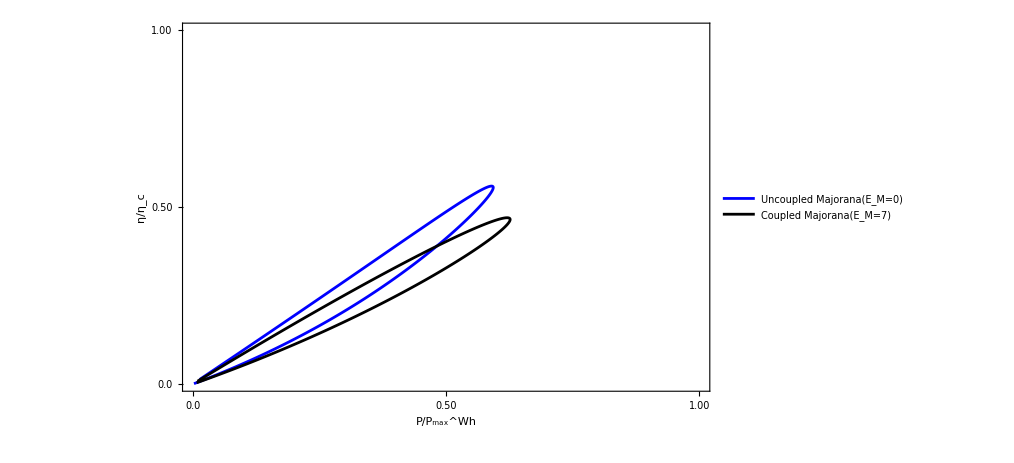

```mathematica
data1=Import["check520.dat"][[All,{3,4}]];
data2=Import["check521.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotLegends->Placed[{Style["Uncoupled Majorana(E_M=0)",Bold,25],Style["Coupled Majorana(E_M=7)",Bold,25]},{Center,Center}],PlotStyle->{Blue,Black},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
T1=2Abs[(4 E^((I (G+1000 ϕ))/2000) p^2 (-2 I E^((I G)/1000+2 I ϕ) x+4 I E^((I (Gf+Vg+2000 ϕ))/1000) x+I E^((I (2 G+Gf+Vg+2000 ϕ))/1000) x-2 I E^((I (G+2 (Gf+Vg+1000 ϕ)))/1000) x+I E^((I (G+Gf+Vg))/1000) x1+2 E^((I G)/1000+I ϕ) y+2 E^((I (G+Gf+Vg+2000 ϕ))/2000) y+2 E^((I (3 G+Gf+Vg+2000 ϕ))/2000) y-2 E^((I (G+3 Gf+3 Vg+2000 ϕ))/2000) y-2 E^((I (3 G+3 Gf+3 Vg+2000 ϕ))/2000) y-2 E^((I (G+2 (Gf+Vg+500 ϕ)))/1000) y+E^((I (3 G+Gf+Vg+4000 ϕ))/2000) (x (-I+x1)-y^2)+E^((I (3 G+3 Gf+3 Vg+4000 ϕ))/2000) (x (-I+x1)-y^2)+E^((3 I (G+Gf+Vg))/2000) (-((-I+x) x1)+y^2)+E^((I (3 G+Gf+Vg))/2000) (-((-I+x) x1)+y^2)+E^((I (G+Gf+Vg+2000 ϕ))/1000) (x (I-2 x1)+2 y^2)+E^((I (2 G+Gf+Vg))/1000) ((I-2 x) x1+2 y^2)+E^((I (G+Gf+Vg+4000 ϕ))/2000) (-2 x (-I+x1)+2 y^2)+E^((I (G+3 Gf+3 Vg+4000 ϕ))/2000) (-2 x (-I+x1)+2 y^2)))/(16 E^((I (Gf+Vg+2000 ϕ))/1000)+8 I E^((I (G+Gf+Vg+4000 ϕ))/2000) (-2 I+x+x1)+8 I E^((I (G+3 Gf+3 Vg+4000 ϕ))/2000) (-2 I+x+x1)-4 E^((I G)/1000+I ϕ) y+4 E^((I G)/1000+3 I ϕ) y-4 E^((3 I (G+Gf+Vg+2000 ϕ))/2000) y-4 E^((I (3 G+Gf+Vg+2000 ϕ))/2000) y+4 E^((I (3 G+3 Gf+3 Vg+2000 ϕ))/2000) y+4 E^((I (3 G+Gf+Vg+6000 ϕ))/2000) y+4 E^((I (G+2 (Gf+Vg+500 ϕ)))/1000) y-4 E^((I (G+2 (Gf+Vg+1500 ϕ)))/1000) y+E^((I (2 G+Gf+Vg))/1000) (x x1-y^2)+E^((I (2 G+Gf+Vg+4000 ϕ))/1000) (x x1-y^2)+8 E^((I (G+Gf+Vg+2000 ϕ))/1000) (2+2 I x1-x (-2 I+x1)+y^2)+E^((I (2 G+Gf+Vg+2000 ϕ))/1000) (-2 x x1+2 y^2)+E^((I G)/1000+2 I ϕ) (4 I x+4 I x1-4 x x1+4 y^2)+E^((I (G+2 (Gf+Vg+1000 ϕ)))/1000) (4 I x+4 I x1-4 x x1+4 y^2)+E^((I (3 G+Gf+Vg+4000 ϕ))/2000) (x (4 I-8 x1)+4 I x1+8 y^2)+E^((I (3 G+3 Gf+3 Vg+4000 ϕ))/2000) (x (4 I-8 x1)+4 I x1+8 y^2))]^2+Abs[(2 E^((I (G+Gf+Vg+1000 ϕ))/2000) (4 E^((I (Gf+Vg+1000 ϕ))/1000)+2 I E^((I (G+Gf+Vg+2000 ϕ))/2000) (-2 I+x+x1)+4 I E^((I (G+3 Gf+3 Vg+2000 ϕ))/2000) (-2 I+x+x1)-E^((I G)/1000) y-E^((I (2 G+Gf+Vg))/1000) y-2 E^((I (3 G+Gf+Vg))/2000) y+E^((I G)/1000+2 I ϕ) y+4 E^((I (Gf+Vg+2000 ϕ))/1000) y+E^((I (2 G+Gf+Vg+2000 ϕ))/1000) y+4 E^((I (G+Gf+Vg+4000 ϕ))/2000) y+2 E^((I (3 G+Gf+Vg+4000 ϕ))/2000) y-4 E^((I (3 G+3 Gf+3 Vg+4000 ϕ))/2000) y-4 E^((I (G+2 (Gf+Vg+1000 ϕ)))/1000) y+E^((I (2 G+Gf+Vg+3000 ϕ))/1000) (x x1-y^2)+E^((I G)/1000+3 I ϕ) (-x x1+y^2)+E^((I G)/1000+I ϕ) (I x1-x (-I+x1)+y^2)+E^((I (2 G+Gf+Vg+1000 ϕ))/1000) (x (I-3 x1)+I x1+3 y^2)+E^((I (3 G+Gf+Vg+2000 ϕ))/2000) (x (2 I-4 x1)+2 I x1+4 y^2)+E^((I (G+2 (Gf+Vg+500 ϕ)))/1000) (4+4 I x+4 I x1-4 x x1+4 y^2)+E^((I (G+Gf+Vg+1000 ϕ))/1000) (8+8 I x+8 I x1-4 x x1+4 y^2)+E^((I (3 G+3 Gf+3 Vg+2000 ϕ))/2000) (4+x (6 I-8 x1)+6 I x1+8 y^2)))/(16 E^((I (Gf+Vg+2000 ϕ))/1000)+8 I E^((I (G+Gf+Vg+4000 ϕ))/2000) (-2 I+x+x1)+8 I E^((I (G+3 Gf+3 Vg+4000 ϕ))/2000) (-2 I+x+x1)-4 E^((I G)/1000+I ϕ) y+4 E^((I G)/1000+3 I ϕ) y-4 E^((3 I (G+Gf+Vg+2000 ϕ))/2000) y-4 E^((I (3 G+Gf+Vg+2000 ϕ))/2000) y+4 E^((I (3 G+3 Gf+3 Vg+2000 ϕ))/2000) y+4 E^((I (3 G+Gf+Vg+6000 ϕ))/2000) y+4 E^((I (G+2 (Gf+Vg+500 ϕ)))/1000) y-4 E^((I (G+2 (Gf+Vg+1500 ϕ)))/1000) y+E^((I (2 G+Gf+Vg))/1000) (x x1-y^2)+E^((I (2 G+Gf+Vg+4000 ϕ))/1000) (x x1-y^2)+8 E^((I (G+Gf+Vg+2000 ϕ))/1000) (2+2 I x1-x (-2 I+x1)+y^2)+E^((I (2 G+Gf+Vg+2000 ϕ))/1000) (-2 x x1+2 y^2)+E^((I G)/1000+2 I ϕ) (4 I x+4 I x1-4 x x1+4 y^2)+E^((I (G+2 (Gf+Vg+1000 ϕ)))/1000) (4 I x+4 I x1-4 x x1+4 y^2)+E^((I (3 G+Gf+Vg+4000 ϕ))/2000) (x (4 I-8 x1)+4 I x1+8 y^2)+E^((I (3 G+3 Gf+3 Vg+4000 ϕ))/2000) (x (4 I-8 x1)+4 I x1+8 y^2))]^2+Abs[(2 E^((I G)/2000+I ϕ) (2 I E^((I (G+Gf+Vg+4000 ϕ))/2000) x-I E^((I (3 G+3 Gf+3 Vg+4000 ϕ))/2000) x-I E^((I (3 G+Gf+Vg))/2000) x1+2 I E^((I (G+3 (Gf+Vg)))/2000) x1-2 E^((I G)/1000+I ϕ) y+4 E^((I (Gf+Vg+1000 ϕ))/1000) y+2 E^((I (G+Gf+Vg+2000 ϕ))/2000) y-2 E^((I (3 G+Gf+Vg+2000 ϕ))/2000) y+2 E^((I (G+3 Gf+3 Vg+2000 ϕ))/2000) y-2 E^((I (3 G+3 Gf+3 Vg+2000 ϕ))/2000) y-2 E^((I (G+2 (Gf+Vg+500 ϕ)))/1000) y+E^((I (2 G+Gf+Vg))/1000) ((-I+x) x1-y^2)+E^((I (2 G+Gf+Vg+2000 ϕ))/1000) (x (-I+x1)-y^2)+E^((I (G+Gf+Vg))/1000) (-((-I+x) x1)+y^2)+E^((I (G+Gf+Vg+2000 ϕ))/1000) (-x (-I+x1)+y^2)+E^((I (3 G+Gf+Vg+4000 ϕ))/2000) (x (I-2 x1)+2 y^2)+E^((3 I (G+Gf+Vg))/2000) ((I-2 x) x1+2 y^2)+E^((I (G+2 (Gf+Vg)))/1000) (-2 (-I+x) x1+2 y^2)+E^((I G)/1000+2 I ϕ) (-2 x (-I+x1)+2 y^2)))/(16 E^((I (Gf+Vg+2000 ϕ))/1000)+8 I E^((I (G+Gf+Vg+4000 ϕ))/2000) (-2 I+x+x1)+8 I E^((I (G+3 Gf+3 Vg+4000 ϕ))/2000) (-2 I+x+x1)-4 E^((I G)/1000+I ϕ) y+4 E^((I G)/1000+3 I ϕ) y-4 E^((3 I (G+Gf+Vg+2000 ϕ))/2000) y-4 E^((I (3 G+Gf+Vg+2000 ϕ))/2000) y+4 E^((I (3 G+3 Gf+3 Vg+2000 ϕ))/2000) y+4 E^((I (3 G+Gf+Vg+6000 ϕ))/2000) y+4 E^((I (G+2 (Gf+Vg+500 ϕ)))/1000) y-4 E^((I (G+2 (Gf+Vg+1500 ϕ)))/1000) y+E^((I (2 G+Gf+Vg))/1000) (x x1-y^2)+E^((I (2 G+Gf+Vg+4000 ϕ))/1000) (x x1-y^2)+8 E^((I (G+Gf+Vg+2000 ϕ))/1000) (2+2 I x1-x (-2 I+x1)+y^2)+E^((I (2 G+Gf+Vg+2000 ϕ))/1000) (-2 x x1+2 y^2)+E^((I G)/1000+2 I ϕ) (4 I x+4 I x1-4 x x1+4 y^2)+E^((I (G+2 (Gf+Vg+1000 ϕ)))/1000) (4 I x+4 I x1-4 x x1+4 y^2)+E^((I (3 G+Gf+Vg+4000 ϕ))/2000) (x (4 I-8 x1)+4 I x1+8 y^2)+E^((I (3 G+3 Gf+3 Vg+4000 ϕ))/2000) (x (4 I-8 x1)+4 I x1+8 y^2))]^2;
Z= (GM  - G-Vg - I*γ )*(GM+G+Vg + I*γ );
x = γ*(G +Vg+I*γ )/Z;
x1 = γ*(G +Vg+ I *γ)/Z;
y = GM*γ/Z;
p=Sqrt[0.5];
Gf=10;
kbT=1;
γ=51;
GM=3;
ϕ=1;
V=20;
f1=1/(1+Exp[(G-Gf+V)/3]);
f2=1/(1+Exp[(G-Gf)/1]);
SetSharedVariable[list1]
list1={};
ParallelDo[{
I1=Re[NIntegrate[T1(f1-f2),{G,Gf,∞}]];
J1=Re[NIntegrate[T1(G-Gf)(f1-f2),{G,Gf,∞}]];
P=Re[V*I1];
η=Re[(10*J1*0.5)/P];
list=AppendTo[list1,{V,Vg,-J1/0.82,η}];
},{Vg,-10.7,60,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check622.dat",list]
```

{651.535,Null}

check622.dat

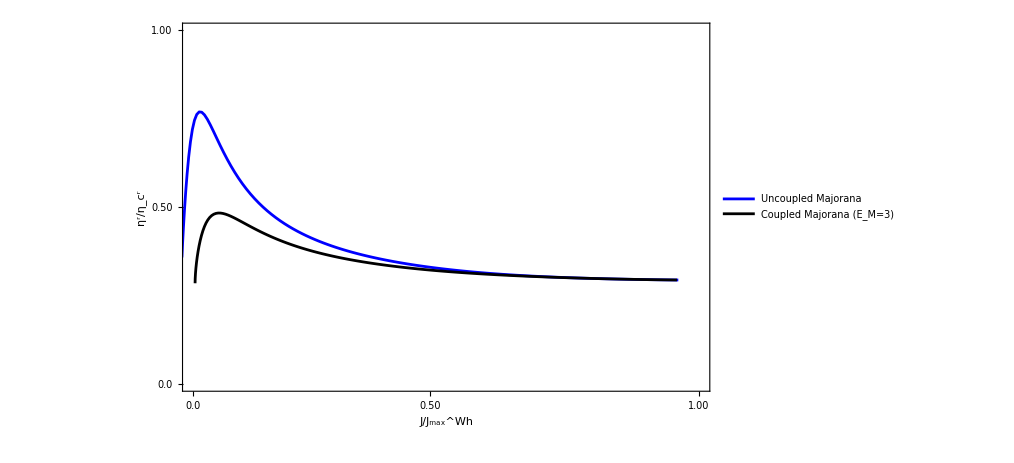

```mathematica
data1=Import["check621.dat"][[All,{3,4}]];
data2=Import["check622.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data1,data2},Frame->True,PlotRange->{{0.059,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0.0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0.059,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["J/J_max^Wh",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},PlotLegends->Placed[{Style["Uncoupled Majorana",Bold,25],Style["Coupled Majorana (E_M=3)",Bold,25]},{Center,Center}],FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Blue,Black},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```